```mathematica
(*Equations A.6 and A.7 n=3*)
Clear[mh,dmh,mw]
mh:=√2
dmh:=0
mw:=mh/2

sol = NDSolve[{a''[r] -(mh^2+dmh^2)*a[r]+(b[r])^2/(4*r)== 0,b''[r]-mw^2*b[r]-(2*b[r])/r^2+mw^2/r*a[r]*b[r]==0,a[0.71]==13.42,a[8.49]==8.40,b[0.71]==9.94,b[8.49]==16.13},{a,b},r, Method->{"Shooting","StartingInitialConditions"->{a[8.49]==8.40,b[8.49]==16.13,a'[8.49]==-0.08,b'[8.49]==-0.15}}];
```

NDSolve::ndsz: At r == 5.11704, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 2.9064, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 2.03622, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: "ndsz" will be suppressed during this calculation.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

NDSolve::berr: There are significant errors {5.84623, -0.828377, -11.322, 1.69927} in the boundary value residuals.  Returning the best solution found.

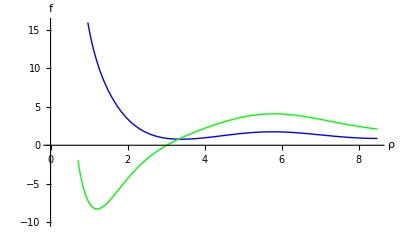

```mathematica
Plot[{Evaluate[a[r] /. sol]/r,Evaluate[b[r] /. sol]/r}, {r,0.71,8.49},PlotStyle->{Blue,Green},AxesLabel->{ρ,f},AxesOrigin->{0,0},PlotRange->{{0,8.49},{-10,16}}]
(*a/r is blue   b/r is green*)
```